```mathematica
a := {{1,6}, {2,5}, {3,7}, {4,10}};
```

```mathematica
getSomeX[list_, property_] := Module[{X,i},
X = list[[1]][[1]];
i =1;
While[i≤Length[list],
X = property[X, list[[i]][[1]] ];
i++;
];
Return[X];
];
```

```mathematica
LinearLeastSquares[values_]:= Module[{i, m},
i = 1;
m = Length[values];

sumX =  Sum[point[[1]], {point, values}];
sumY =  Sum[point[[2]], {point, values}];
sumXY =  Sum[point[[1]] * point[[2]], {point, values}];
sumXX =  Sum[point[[1]] * point[[1]], {point, values}];

a0 = (sumXX*sumY - sumXY * sumX) /  (m * sumXX - (sumX) ^ 2);
a1 = (m * sumXY - sumX*sumY) / (m * sumXX -  (sumX) ^ 2);

e2 = Sum[(point[[2]] - (a1 * point[[1]] + a0)) ^ 2, {point, values}];

Return[{N[a0] , N[a1], N[e2]}];
]
```

```mathematica
result = LinearLeastSquares[a];
f[x_] := result[[2]] * x + result[[1]] ;
```

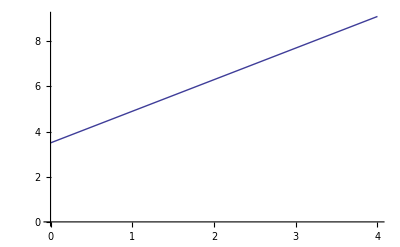

```mathematica
functionPlot = Plot[f[x], {x, 0, getSomeX[a, Max]}, AxesOrigin->{0,0}]
```

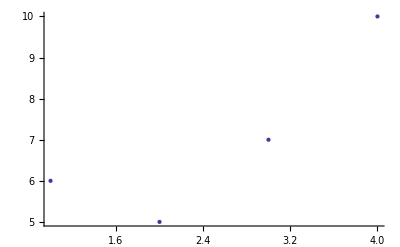

```mathematica
pointsPlot = ListPlot[a, AxesOrigin->{0,0}]
```

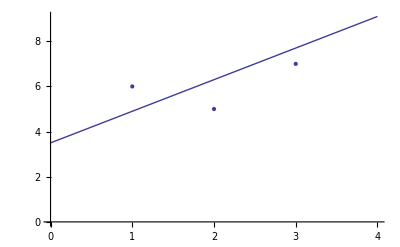

```mathematica
Show[functionPlot, pointsPlot]
```